```mathematica
e1[t_]:=-D[H[t],t]/H[t]^2
D[e1[t],t]/(H[t]e1[t])//FullSimplify
```

(-2 H'[t]^2+H[t] H''[t])/(H[t]^2 H'[t])

```mathematica
PieChart[{10.9,22.4,14.7,51.9-27.2,27.2}]
```

-Graphics-

```mathematica
27.2+9.4+2.1+1.1+.8+.8+.7+.6
10.2+5.1+4.9+3.8+3.6+3.5+3.2+2.3+1.7+1.2+1.0+1.0+.9
1.3+.6
```

42.7

42.4

1.9

```mathematica
%+%%+%%%
```

87.

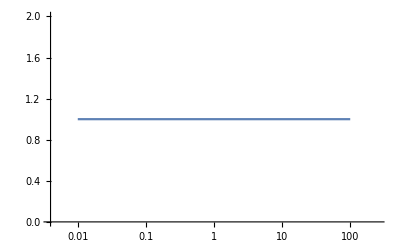

```mathematica
LogLinearPlot[Abs[x^I],{x,0.01,100}]
```

```mathematica
x^I//FullSimplify
```

x^ⅈ

```mathematica
Exp[I Log[x]]
```

x^ⅈ

```mathematica
?Divisible
```

Divisible[n,m] yields True if n is divisible by m, and yields False if it is not.

```mathematica
ndiv=Function[x,Length@Select[Range[100],Divisible[#,x]||Divisible[x,#]&]-1]
```

Function[x,Length[Select[Range[100],Divisible[#1,x]||Divisible[x,#1]&]]-1]

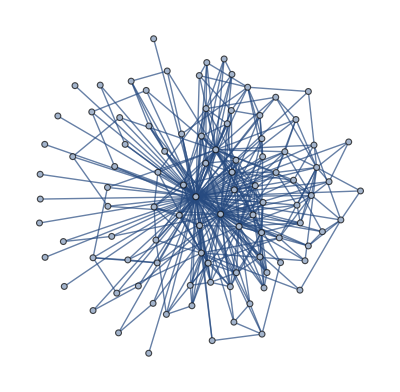

```mathematica
g=Graph[UndirectedEdge@@@Select[Tuples[Range[100],2],(#[[1]]≠#[[2]])&&Divisible@@#&]]
```

```mathematica
NN=5;
Graph[Select[EdgeList[g],ndiv[#[[1]]]>NN&&ndiv[#[[2]]]>NN&]];
FindShortestTour@%
```

{45,{2,40,80,16,64,32,8,56,28,14,84,21,42,7,70,10,20,60,15,45,90,18,72,36,9,54,3,12,48,96,24,4,44,88,22,66,11,1,13,78,6,30,5,100,50,2}}

```mathematica
{45,{2,40,80,16,64,32,8,56,28,14,84,21,42,7,70,10,20,60,15,45,90,18,72,36,9,54,3,12,48,96,24,4,44,88,22,66,11,1,13,78,6,30,5,100,50,2}}
```

```mathematica
Length[{2,40,80,16,64,32,8,56,28,14,84,21,42,7,70,10,20,60,15,45,90,18,72,36,9,54,3,12,48,96,24,4,44,88,22,66,11,1,13,78,6,30,5,100,50}]
```

45

```mathematica
CopyToClipboard["2,40,80,16,64,32,8,56,28,14,84,21,42,7,70,10,20,60,15,45,90,18,72,36,9,54,3,12,48,96,24,4,44,88,22,66,11,1,13,78,6,30,5,100,50"]
```

```mathematica
?FindShortestPath
```

RowBox[{"FindShortestPath", "[", RowBox[{StyleBox["g", "TI"], ",", StyleBox["s", "TI"], ",", StyleBox["t", "TI"]}], "]"}] finds the shortest path from source vertex StyleBox["s", "TI"] to target vertex StyleBox["t", "TI"] in the graph StyleBox["g", "TI"].
RowBox[{"FindShortestPath", "[", RowBox[{StyleBox["g", "TI"], ",", StyleBox["s", "TI"], ",", "All"}], "]"}] generates a RowBox[{"ShortestPathFunction", "[", StyleBox["…", "TR"], "]"}] that can be applied repeatedly to different StyleBox["t", "TI"].
RowBox[{"FindShortestPath", "[", RowBox[{StyleBox["g", "TI"], ",", "All", ",", StyleBox["t", "TI"]}], "]"}] generates a RowBox[{"ShortestPathFunction", "[", StyleBox["…", "TR"], "]"}] that can be applied repeatedly to different StyleBox["s", "TI"].
RowBox[{"FindShortestPath", "[", RowBox[{StyleBox["g", "TI"], ",", "All", ",", "All"}], "]"}] generates a RowBox[{"ShortestPathFunction", "[", StyleBox["…", "TR"], "]"}] that can be applied to different StyleBox["s", "TI"] and StyleBox["t", "TI"].

```mathematica
Length[{2,866,433,339,678,226,452,904,905,181,543,747,249,498,996,332,664,166,830,415,83,913,914,457,835,167,501,989,771,257,514,781,889,127,635,634,317,951,717,239,478,956,939,313,626,637,91,455,910,182,364,728,104,520,260,780,156,78,546,273,819,117,351,702,234,468,936,312,624,208,16,944,472,236,708,354,6,534,267,801,671,366,732,244,488,976,122,854,427,61,610,305,915,183,549,964,482,241,723,3,381,762,254,508,849,283,566,899,979,473,946,86,344,688,172,860,430,215,645,129,516,258,774,387,9,531,177,885,295,590,118,826,413,59,767,633,211,844,422,892,446,223,669,353,706,362,724,778,389,753,251,502,963,321,642,214,856,428,107,535,5,955,191,573,649,11,583,542,271,813,343,686,98,490,70,350,700,140,280,840,168,336,84,420,105,525,175,875,125,625,961,31,341,682,62,992,496,248,744,372,186,558,279,837,93,651,217,434,868,124,620,310,930,465,155,775,711,237,474,948,316,632,158,790,395,79,553,554,277,831,698,349,524,262,786,393,131,655,453,906,302,604,151,755,943,23,667,917,466,932,233,699,893,386,772,193,579,437,874,46,598,299,897,69,621,207,414,828,138,276,552,184,736,368,92,644,322,966,483,161,805,115,575,25,725,145,580,290,870,435,449,898,614,307,921,799,931,49,539,77,847,121,605,55,935,85,425,850,50,500,250,1000,200,600,300,150,750,375,75,825,275,550,110,330,990,495,165,660,220,440,880,176,352,32,416,832,64,704,88,616,308,924,132,528,264,66,396,792,198,594,297,891,99,693,231,462,154,770,385,35,595,17,697,41,533,895,707,101,505,949,916,458,229,687,851,934,467,791,113,565,685,137,411,822,274,548,4,668,334,451,902,82,574,287,861,123,369,738,246,492,984,328,656,164,820,410,205,615,15,345,690,230,920,460,20,100,800,400,80,560,112,448,896,224,672,48,240,960,192,576,288,72,18,36,216,648,162,324,108,432,864,144,24,96,384,768,256,512,128,640,320,40,160,480,120,30,60,12,564,282,846,423,141,705,235,470,940,188,752,376,94,658,329,987,21,903,301,602,43,731,447,894,298,596,149,745,802,401,993,331,662,511,695,139,556,278,834,417,703,862,431,628,314,942,471,157,785,721,103,515,527,529,597,199,796,398,1,469,938,14,994,497,7,679,97,485,970,10,370,740,148,592,296,888,444,222,666,333,999,27,783,261,522,174,348,696,232,928,464,116,812,406,203,609,87,957,319,638,22,814,407,388,776,194,582,291,873,519,173,865,611,47,517,995,871,959,958,479,718,359,749,764,382,383,766,365,730,146,584,292,876,438,219,657,73,803,869,559,591,589,581,974,487,545,109,763,394,788,197,985,461,922,923,71,639,213,426,852,284,568,142,710,355,815,163,652,326,978,489,409,818,817,19,551,29,493,986,58,754,377,379,758,807,269,538,403,806,26,338,676,52,572,286,858,429,143,715,65,390,130,650,325,975,195,585,45,405,810,135,675,225,900,450,90,360,720,180,540,270,54,486,972,243,729,81,567,189,945,315,630,210,42,252,504,126,756,378,63,441,882,294,588,147,735,245,980,196,784,392,56,28,532,266,798,399,133,665,95,475,950,190,380,760,152,608,304,912,456,228,684,342,114,570,285,855,171,513,57,627,209,418,836,76,988,494,247,741,623,89,445,890,178,712,356,925,185,555,111,777,259,518,74,962,481,37,629,779,927,309,618,206,824,412,746,373,371,742,106,530,265,795,159,477,954,318,636,212,848,424,8,872,436,218,654,327,981,982,491,454,908,227,681,909,303,606,202,404,808,537,179,358,716,926,463,973,793,794,397,692,346,347,694,622,311,933,998,499,562,281,843,965,901,53,689,13,845,169,507,39,663,221,442,884,68,340,680,170,510,255,765,153,459,918,306,612,102,408,204,816,272,544,136,952,476,238,714,357,119,833,391,782,34,578,289,867,367,734,737,67,603,201,402,804,268,536,134,670,335,337,674,713,361,722,38,646,323,969,51,561,187,374,748,44,484,968,242,726,363,33,759,253,506,886,443,586,293,879,878,439,421,842,841,838,419,789,263,526,2}]
```

928

```mathematica
Select[Range[1000],PrimeQ[#]&&#>500&]
```

{503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997}